```mathematica
Prova di Mathematica
```

di Mathematica Prova

```mathematica
Somma di due numeri
```

di due numeri Somma

```mathematica
a = 2 + 4 (*somma di due numeri*)
```

6

```mathematica
Pippo
```

Pippo

```mathematica
b := pippo
```

```mathematica
b
```

pippo

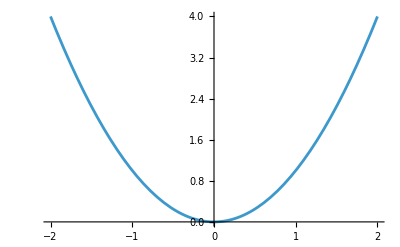

```mathematica
Plot[x^2, {x,-2,2}]
```

```mathematica
Series[Exp[x], {x,0,6}] (*espansione in serie di Taylor*)
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+O[x]^7

```mathematica
Integrate[x^3,  {x, -2, 2}] (*integrale definito di una funzione*)
```

0

```mathematica
FullForm[ %41 ]
```

SeriesData[x,0,List[1,1,Rational[1,2],Rational[1,6],Rational[1,24],Rational[1,120],Rational[1,720]],0,7,1]

```mathematica
FullForm[ %44 ]
```

SeriesData[x,0,List[1,1,Rational[1,2],Rational[1,6],Rational[1,24],Rational[1,120],Rational[1,720]],0,7,1]

```mathematica
lista := {0,1,2,3,4,5}
```

List

```mathematica
lista[[0]] (*la doppia parentesi quadra restituisce l'elemento di una lista*)
```

List

```mathematica
expr=(r+s)(x+y)(w+z)
```

(r+s) (x+y) (w+z)

```mathematica
FullForm[expr] (*FullForm ci consente di indagare la rappresentazione interna di un'espressione*)
```

Times[Plus[r,s],Plus[x,y],Plus[w,z]]

```mathematica
expr[[3,0]]
```

Plus

```mathematica
expr /. {r -> diocane}
```

```mathematica
(diocane+s) (x+y) (w+z)
```

```mathematica
Clear[a, b] (*a cosa serve la funzione Clear? Per pulire i valori delle due variabili 'a' e 'b'*)
```

```mathematica
sol = Solve[ 3 x^2 + 6x^2 - 5 == 0, x]
```

{{x→-(√5)/3},{x→(√5)/3}}

```mathematica
x /. sol (*estrae i valori delle soluzioni in una lista pulita*)
```

{-(√5)/3,(√5)/3}

```mathematica
sol2 = Solve[{x^2+y^2==1,x^2-y^2==1 },{x,y}]
```

{{x→-1,y→0},{x→1,y→0}}

```mathematica
{x, y}/. sol2
```

{{-1,0},{1,0}}

Risoluzione di un sistema lineare di equazioni

```mathematica
sol3 = Solve[{a x + b y == k1, c x + d y == k2}, {x,y}]
```

{{x→-(d k1-b k2)/(b c-a d),y→-(-c k1+a k2)/(b c-a d)}}

usando le matrici

```mathematica
M := {{a, b}, {c, d}}
inc := {x, y}
known := {k1, k2}
Solve[ M.inc == known , inc]
```

{{x→-(d k1-b k2)/(b c-a d),y→-(-c k1+a k2)/(b c-a d)}}

```mathematica
M.inc
M.known (*prodotti matrice per vettori colonna*)
```

{a x+b y,c x+d y}

{a k1+b k2,c k1+d k2}

```mathematica
inc.M
known.M (*prodotti vettori riga per matrice*)
```

{a x+c y,b x+d y}

{a k1+c k2,b k1+d k2}

```mathematica
inc known
```

{k1 x,k2 y}

```mathematica
(*in questo caso la funzione Normal tronca i termini di ordine superiore a n*)
serie[n_] = Normal[ Series[ Log[1+x], {x,0,n}] ]
```

Series::serlim: Series order specification n is not a machine-sized integer.

Log[1+x]

```mathematica
serie /. x->-0.9
```

serie

```mathematica
Clear[serie]
```

```mathematica
Do[ 
numerico = serie[n]/.x->-0.9;
errore = Abs[ numerico/Log[0.1] -1];
Print[n,"  ",errore],
{n,1,100}]
```

1  Abs[-1-0.434294 serie[1]]

2  Abs[-1-0.434294 serie[2]]

3  Abs[-1-0.434294 serie[3]]

4  Abs[-1-0.434294 serie[4]]

5  Abs[-1-0.434294 serie[5]]

6  Abs[-1-0.434294 serie[6]]

7  Abs[-1-0.434294 serie[7]]

8  Abs[-1-0.434294 serie[8]]

9  Abs[-1-0.434294 serie[9]]

10  Abs[-1-0.434294 serie[10]]

11  Abs[-1-0.434294 serie[11]]

12  Abs[-1-0.434294 serie[12]]

13  Abs[-1-0.434294 serie[13]]

14  Abs[-1-0.434294 serie[14]]

15  Abs[-1-0.434294 serie[15]]

16  Abs[-1-0.434294 serie[16]]

17  Abs[-1-0.434294 serie[17]]

18  Abs[-1-0.434294 serie[18]]

19  Abs[-1-0.434294 serie[19]]

20  Abs[-1-0.434294 serie[20]]

21  Abs[-1-0.434294 serie[21]]

22  Abs[-1-0.434294 serie[22]]

23  Abs[-1-0.434294 serie[23]]

24  Abs[-1-0.434294 serie[24]]

25  Abs[-1-0.434294 serie[25]]

26  Abs[-1-0.434294 serie[26]]

27  Abs[-1-0.434294 serie[27]]

28  Abs[-1-0.434294 serie[28]]

29  Abs[-1-0.434294 serie[29]]

30  Abs[-1-0.434294 serie[30]]

31  Abs[-1-0.434294 serie[31]]

32  Abs[-1-0.434294 serie[32]]

33  Abs[-1-0.434294 serie[33]]

34  Abs[-1-0.434294 serie[34]]

35  Abs[-1-0.434294 serie[35]]

36  Abs[-1-0.434294 serie[36]]

37  Abs[-1-0.434294 serie[37]]

38  Abs[-1-0.434294 serie[38]]

39  Abs[-1-0.434294 serie[39]]

40  Abs[-1-0.434294 serie[40]]

41  Abs[-1-0.434294 serie[41]]

42  Abs[-1-0.434294 serie[42]]

43  Abs[-1-0.434294 serie[43]]

44  Abs[-1-0.434294 serie[44]]

45  Abs[-1-0.434294 serie[45]]

46  Abs[-1-0.434294 serie[46]]

47  Abs[-1-0.434294 serie[47]]

48  Abs[-1-0.434294 serie[48]]

49  Abs[-1-0.434294 serie[49]]

50  Abs[-1-0.434294 serie[50]]

51  Abs[-1-0.434294 serie[51]]

52  Abs[-1-0.434294 serie[52]]

53  Abs[-1-0.434294 serie[53]]

54  Abs[-1-0.434294 serie[54]]

55  Abs[-1-0.434294 serie[55]]

56  Abs[-1-0.434294 serie[56]]

57  Abs[-1-0.434294 serie[57]]

58  Abs[-1-0.434294 serie[58]]

59  Abs[-1-0.434294 serie[59]]

60  Abs[-1-0.434294 serie[60]]

61  Abs[-1-0.434294 serie[61]]

62  Abs[-1-0.434294 serie[62]]

63  Abs[-1-0.434294 serie[63]]

64  Abs[-1-0.434294 serie[64]]

65  Abs[-1-0.434294 serie[65]]

66  Abs[-1-0.434294 serie[66]]

67  Abs[-1-0.434294 serie[67]]

68  Abs[-1-0.434294 serie[68]]

69  Abs[-1-0.434294 serie[69]]

70  Abs[-1-0.434294 serie[70]]

71  Abs[-1-0.434294 serie[71]]

72  Abs[-1-0.434294 serie[72]]

73  Abs[-1-0.434294 serie[73]]

74  Abs[-1-0.434294 serie[74]]

75  Abs[-1-0.434294 serie[75]]

76  Abs[-1-0.434294 serie[76]]

77  Abs[-1-0.434294 serie[77]]

78  Abs[-1-0.434294 serie[78]]

79  Abs[-1-0.434294 serie[79]]

80  Abs[-1-0.434294 serie[80]]

81  Abs[-1-0.434294 serie[81]]

82  Abs[-1-0.434294 serie[82]]

83  Abs[-1-0.434294 serie[83]]

84  Abs[-1-0.434294 serie[84]]

85  Abs[-1-0.434294 serie[85]]

86  Abs[-1-0.434294 serie[86]]

87  Abs[-1-0.434294 serie[87]]

88  Abs[-1-0.434294 serie[88]]

89  Abs[-1-0.434294 serie[89]]

90  Abs[-1-0.434294 serie[90]]

91  Abs[-1-0.434294 serie[91]]

92  Abs[-1-0.434294 serie[92]]

93  Abs[-1-0.434294 serie[93]]

94  Abs[-1-0.434294 serie[94]]

95  Abs[-1-0.434294 serie[95]]

96  Abs[-1-0.434294 serie[96]]

97  Abs[-1-0.434294 serie[97]]

98  Abs[-1-0.434294 serie[98]]

99  Abs[-1-0.434294 serie[99]]

100  Abs[-1-0.434294 serie[100]]